# Motivations-Plots Dirac

```mathematica
(* Dirac und freunde *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
rtilde = Subscript[r̃, 0];
(* axstyle= Directive[Thickness[0.015/2], Gray]; *)
```

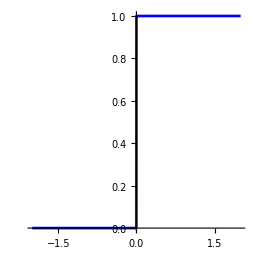

```mathematica
heavi=Plot[ HeavisideTheta[r],
{r,-2,2},
PlotStyle-> {Thickness[0.015/2],Blue},
PlotRange-> {0,1},
Exclusions-> None,
AspectRatio-> 1,
ImageSize-> 9cm(*,
AxesStyle-> axstyle*)
]
```

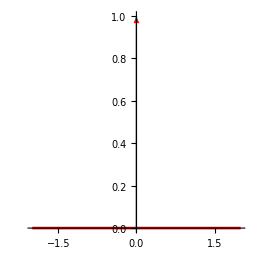

```mathematica
dirac=Plot[0, {r,-2,2}, 
PlotStyle :> {Thickness[0.015/2],Red},
Epilog-> {Red,Thick,Arrow[{{0,0},{0,1}}]},
AspectRatio-> 1,
PlotRange-> {0,1},
ImageSize-> 9cm(*,
AxesStyle-> axstyle*)
]
```

```mathematica
Export["../figures/diracH-heaviside.pdf", heavi, ImageResolution-> 400]
Export["../figures/diracH-dirac.pdf", dirac, ImageResolution-> 400]
```

../figures/diracH-heaviside.pdf

../figures/diracH-dirac.pdf

## Holo

```mathematica
h[r_]=r^2/(r^2+1)
```

r^2/(1+r^2)

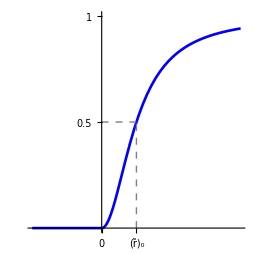

```mathematica
holoHeavi=Plot[ 
If[r≤ 0,0,h[r]],
{r,-2,4},
PlotStyle-> {Thickness[0.015/2],Blue},
AspectRatio-> 1,
ImageSize-> 9cm,
PlotRange-> {0,1},
Ticks-> {{{0,0},{1,rtilde}}, {{0.5,"0.5"},{1,"1"}}},
Epilog-> {
Thick, Gray, Dashed,
Line@{{1,0},{1,0.5}},
Line@{{0,0.5},{1,0.5}}
}(*,
AxesStyle->axstyle*)
]
```

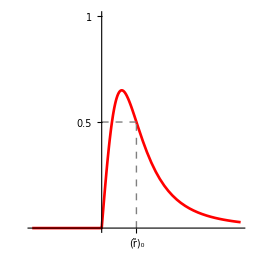

```mathematica
hD[r_]=D[h[r],r];
holoD=Plot[ 
If[r≤ 0,0,hD[r]],
{r,-2,4},
PlotStyle-> {Thickness[0.015/2],Red},
AspectRatio-> 1,
ImageSize-> 9cm,
PlotRange-> {0,1},
Ticks-> {{{1,rtilde}}, {{0.5,"0.5"},{1,"1"}}},
Epilog-> {
Thick, Gray, Dashed,
Line@{{1,0},{1,0.5}},
Line@{{0,0.5},{1,0.5}}
}(*,
AxesStyle-> axstyle*)
]
```

```mathematica
Export["../figures/diracH-holo.pdf", holoHeavi, ImageResolution-> 400]
Export["../figures/diracH-dholo.pdf", holoD, ImageResolution-> 400]
```

../figures/diracH-holo.pdf

../figures/diracH-dholo.pdf